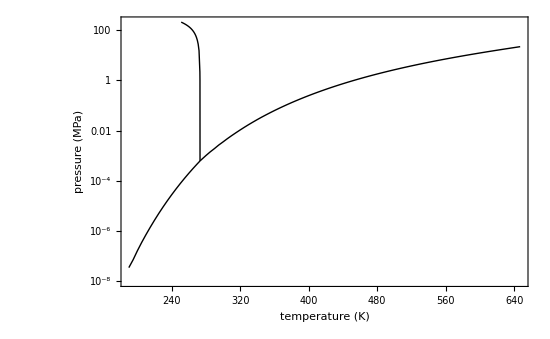

```mathematica
sub={{190.,3.4*^-8},{195.,7.*^-8},{200.,1.6*^-7},{205.,3.43*^-7},{210.,7.*^-7},{215.,1.381*^-6},{220.,2.65*^-6},{225.,4.94*^-6},{230.,8.95*^-6},{235.,0.00001581},{240.,0.00002727},{245.,0.00004601},{250.,0.00007603},{255.,0.00012316},{260.,0.00019583},{265.,0.00030594},{270.,0.00047008},{273.16,0.00061166}};
sat={{273.16,0.00061},{275.,0.0007},{280.,0.001},{285.,0.0014},{290.,0.0019},{295.,0.00263},{300.,0.0035},{305.,0.0047},{310.,0.00621},{315.,0.0081},{320.,0.0105},{325.,0.0135},{330.,0.0172},{335.,0.0217},{340.,0.02722},{345.,0.03384},{350.,0.0417},{355.,0.0511},{360.,0.06225},{365.,0.0753},{370.,0.09051},{375.,0.10831},{380.,0.12891},{385.,0.1525},{390.,0.1796},{395.,0.2106},{400.,0.24582},{405.,0.2856},{410.,0.3304},{415.,0.3808},{420.,0.43723},{425.,0.5002},{430.,0.5702},{435.,0.6478},{440.,0.7335},{445.,0.82811},{450.,0.932},{455.,1.046},{460.,1.1707},{465.,1.3067},{470.,1.4548},{475.,1.61571},{480.,1.7902},{485.,1.9789},{490.,2.18283},{495.,2.40253},{500.,2.6389},{505.,2.8929},{510.,3.1652},{515.,3.4569},{520.,3.76874},{525.,4.1016},{530.,4.45675},{535.,4.83471},{540.,5.2367},{545.,5.6639},{550.,6.11711},{555.,6.5974},{560.,7.10615},{565.,7.6443},{570.,8.2131},{575.,8.8138},{580.,9.44771},{585.,10.11621},{590.,10.8208},{595.,11.5629},{600.,12.3443},{605.,13.1667},{610.,14.032},{615.,14.94241},{620.,15.9002},{625.,16.9081},{630.,17.9691},{635.,19.0868},{640.,20.26592},{645.,21.51413},{647.096,22.064}};

ice={{251.1652,209.8985},{252.,203.53572},{253.,195.86442},{254.,188.1245},{255.,180.30192},{256.,172.3814},{257.,164.3468},{258.,156.18111},{259.,147.866},{260.,139.3821},{261.,130.7087},{262.,121.8238},{263.,112.70411},{264.,103.32431},{265.,93.6579},{266.,83.6765},{267.,73.34961},{268.,62.645},{269.,51.5281},{270.,39.962},{271.,27.90752},{272.,15.32261},{273.,2.1627},{273.1,1.},{273.16,0.00061}};

p2=ListLogPlot[{sub,sat,ice},Joined->True,PlotStyle->{{Thick,Black}},Frame->True,FrameLabel->{Style["temperature (K)",17],Style["pressure  (MPa)",17]},LabelStyle->{Black,14},ImageSize->550]
```